# Settings

```mathematica
h=0.004;
plotSize=600;
plotSizeLong=450*2;
th=0.005;
scaleX=1;
scaleY=1;
pointSize=Medium
markerSize=10;
fontSize=22;
fontSizeLegend=18;
numberOfDigits=2;
aspectRatio=8/10;
markers={{"●",markerSize},{"■",markerSize}};

plotSettingsLine={PlotStyle->{Thickness[th],Red}
,Frame-> True
,FrameStyle->Directive[Thickness[th],Bold,22]
,ImageSize->plotSize
,Axes->False}

plotSettingsLineTens={PlotStyle->{Thickness[th],Dashed, Blue}
,Frame-> True
,FrameStyle->Directive[Thickness[th],Bold,22]
,ImageSize->plotSize
,Axes->False}

plotSettingsLineVec={PlotStyle->{Thickness[th],Dashed, Brown}
,Frame-> True
,FrameStyle->Directive[Thickness[th],Bold,22]
,ImageSize->plotSize
,Axes->False}

plotSettings={LabelStyle->Directive[Bold,fontSize,"Times"]
,PlotStyle->PointSize[pointSize]
,PlotMarkers->{Automatic,markerSize}
,Frame-> True
,FrameStyle->Directive[Thickness[th],Bold,22]
,ImageSize->plotSize
,Axes->False}

Needs["ErrorBarPlots`"]
```

Medium

{PlotStyle→{Thickness[0.005],RGBColor[1, 0, 0]},Frame→True,FrameStyle→Directive[Thickness[0.005],Bold,22],ImageSize→600,Axes→False}

{PlotStyle→{Thickness[0.005],Dashing[{Small,Small}],RGBColor[0, 0, 1]},Frame→True,FrameStyle→Directive[Thickness[0.005],Bold,22],ImageSize→600,Axes→False}

{PlotStyle→{Thickness[0.005],Dashing[{Small,Small}],RGBColor[0.6, 0.4, 0.2]},Frame→True,FrameStyle→Directive[Thickness[0.005],Bold,22],ImageSize→600,Axes→False}

{LabelStyle→Directive[Bold,22,Times],PlotStyle→PointSize[Medium],PlotMarkers→{Automatic,10},Frame→True,FrameStyle→Directive[Thickness[0.005],Bold,22],ImageSize→600,Axes→False}

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

# Малые смещения

```mathematica
lens[F_]:=({{1, 0}, {-1/F, 1}});
freespace[L_]:=({{1, L}, {0, 1}});
λ=1064*10^-9;
w0=2.5*10^-3;
q1=I(π w0^2)/λ;
f[q0_,ABCD_]:=Module[{q,rel,z0,wz,wz0},
q=(ABCD[[1,1]]q0+ABCD[[1,2]])/(ABCD[[2,1]]q0+ABCD[[2,2]]);
rel=ComplexExpand[Re[1/q]];
z0=Quiet[Solve[rel==0,x]];
wz=√(-λ/(π ComplexExpand[Im[1/q]]));
wz0=wz/.z0;
Flatten[{wz,N[z0],N[wz0]}]
]
```

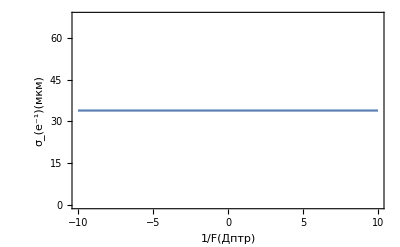

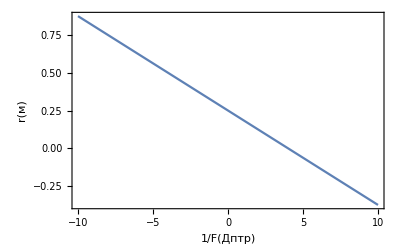

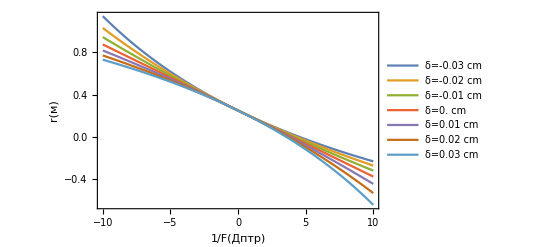

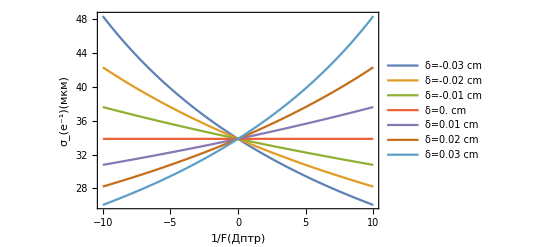

Plot::nonopt: Options expected (instead of plotSettingsLine) beyond position 2 in Plot[{(x finder[q1,freespace[x].lens[Fs].freespace[Plus[«2»]].lens[Times[«2»]]]⟦2⟧)/0.1^6,(x finder[q1,«1»]⟦2⟧)/0.1^6,x/(0.1^6[q1,«1»]⟦2⟧),(x«1»finder[q1,«1»]«1»«1»⟧)/0.1^6,(x finder[q1,«1»]⟦2⟧)/0.1^6,(x «1»⟦2⟧)/0.1^6,(x finder[q1,freespace[x].lens[Fs].freespace[Plus[«2»]].lens[Times[«2»]]]⟦2⟧)/0.1^6},«3»,PlotLegends→«1»]. An option must be a rule or a list of rules.

Plot::nonopt: Options expected (instead of plotSettingsLine) beyond position 2 in Plot[«1»]. An option must be a rule or a list of rules.

Plot[{x/.finder[q1,freespace[x].lens[Fs].freespace[Fs-0.03].lens[1/kk]]⟦2⟧,x/.finder[q1,freespace[x].lens[Fs].freespace[Fs-0.02].lens[1/kk]]⟦2⟧,x/.finder[q1,freespace[x].lens[Fs].freespace[Fs-0.01].lens[1/kk]]⟦2⟧,x/.finder[q1,freespace[x].lens[Fs].freespace[Fs].lens[1/kk]]⟦2⟧,x/.finder[q1,freespace[x].lens[Fs].freespace[Fs+0.01].lens[1/kk]]⟦2⟧,x/.finder[q1,freespace[x].lens[Fs].freespace[Fs+0.02].lens[1/kk]]⟦2⟧,x/.finder[q1,freespace[x].lens[Fs].freespace[Fs+0.03].lens[1/kk]]⟦2⟧},{kk,-10,10},plotSettingsLine,FrameLabel→{1/F(Дптр),r(м)},PlotLegends→Table[δ=<>ToString[i]<> cm,{i,-0.03,0.03,0.01}]]

```mathematica
Fs=0.25;
Plot[10^6 f[q1,freespace[x].lens[Fs].freespace[Fs].lens[1/kk]][[3]],{kk,-10,10},Frame->True,FrameLabel->{"1/F(Дптр)","σ_(e^-1)(мкм)"},PlotLegends->Table["δ="<>ToString[i]<>" cm", 0]]

Plot[x/.f[q1,freespace[x].lens[Fs].freespace[Fs].lens[1/kk]][[2]],{kk,-10,10},Frame->True, FrameLabel->{"1/F(Дптр)","r(м)"},PlotLegends->Table["δ="<>ToString[i]<>" cm",0]]

Plot[{x/.f[q1,freespace[x].lens[Fs].freespace[Fs-0.03].lens[1/kk]][[2]],x/.f[q1,freespace[x].lens[Fs].freespace[Fs-0.02].lens[1/kk]][[2]],x/.f[q1,freespace[x].lens[Fs].freespace[Fs-0.01].lens[1/kk]][[2]],x/.f[q1,freespace[x].lens[Fs].freespace[Fs].lens[1/kk]][[2]],x/.f[q1,freespace[x].lens[Fs].freespace[Fs+0.01].lens[1/kk]][[2]],x/.f[q1,freespace[x].lens[Fs].freespace[Fs+0.02].lens[1/kk]][[2]],x/.f[q1,freespace[x].lens[Fs].freespace[Fs+0.03].lens[1/kk]][[2]]},{kk,-10,10},Frame->True, FrameLabel->{"1/F(Дптр)","r(м)"},PlotLegends->Table["δ="<>ToString[i]<>" cm",{i,-0.03,0.03,0.01}]]

Plot[{  10^6 f[q1,freespace[x].lens[Fs].freespace[Fs-0.03].lens[1/kk]][[3]], 10^6 f[q1,freespace[x].lens[Fs].freespace[Fs-0.02].lens[1/kk]][[3]],  10^6 f[q1,freespace[x].lens[Fs].freespace[Fs-0.01].lens[1/kk]][[3]], 10^6 f[q1,freespace[x].lens[Fs].freespace[Fs].lens[1/kk]][[3]], 10^6 f[q1,freespace[x].lens[Fs].freespace[Fs+0.01].lens[1/kk]][[3]], 10^6 f[q1,freespace[x].lens[Fs].freespace[Fs+0.02].lens[1/kk]][[3]],10^6 f[q1,freespace[x].lens[Fs].freespace[Fs+0.03].lens[1/kk]][[3]]},{kk,-10,10},Frame->True,FrameLabel->{"1/F(Дптр)","σ_(e^-1)(мкм)"},PlotLegends->Table["δ="<>ToString[i]<>" cm",{i,-0.03,0.03,0.01}]]
```

# Транспорт

0.01

100

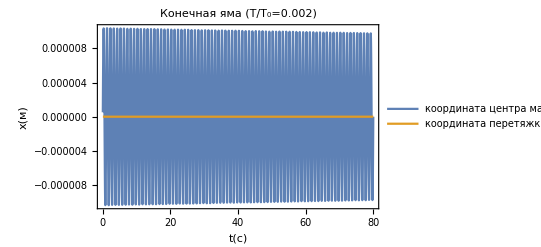

9.28064×10^-6

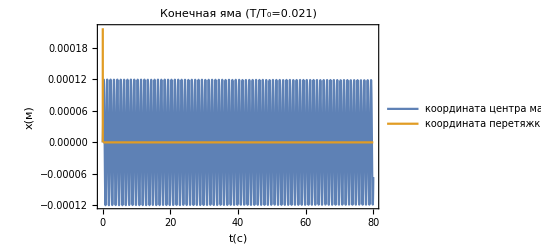

0.000114097

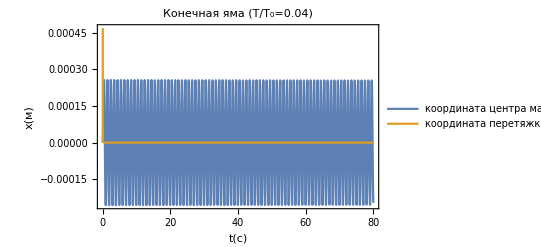

0.000252454

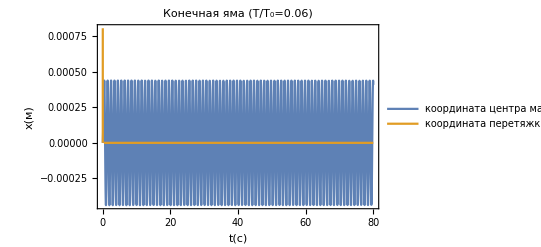

0.000436305

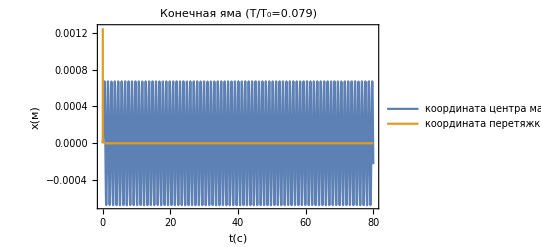

0.000671229

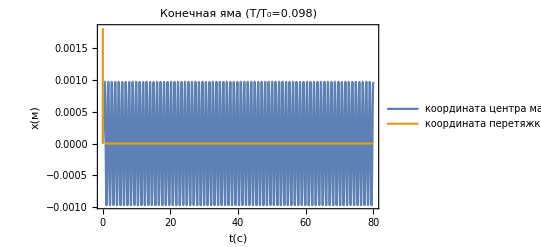

0.000963835

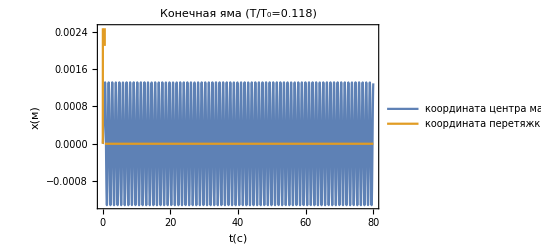

0.00131695

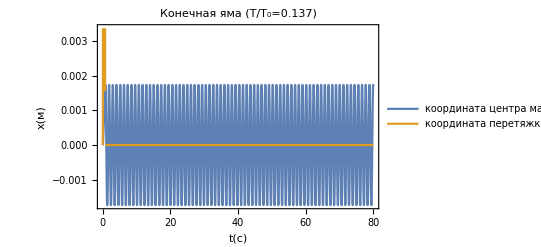

0.00171657

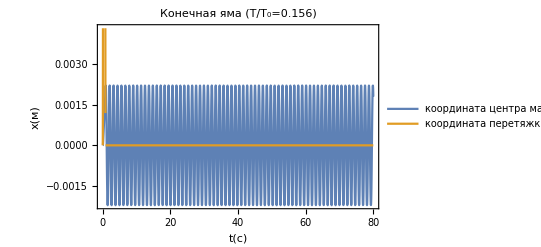

0.00220911

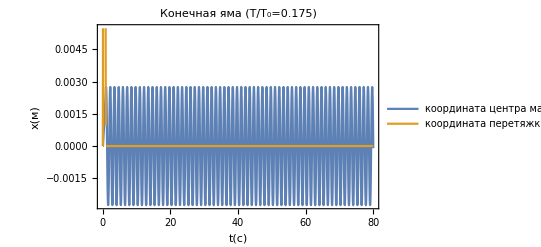

0.00274334

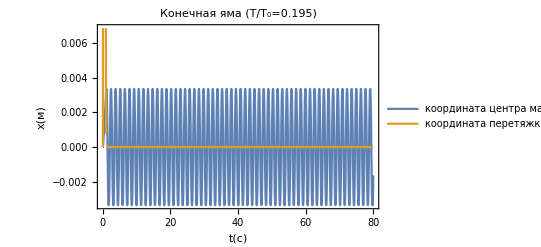

0.00335344

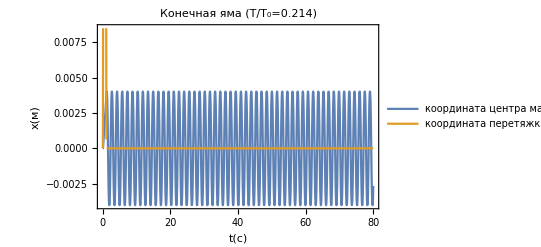

0.00402348

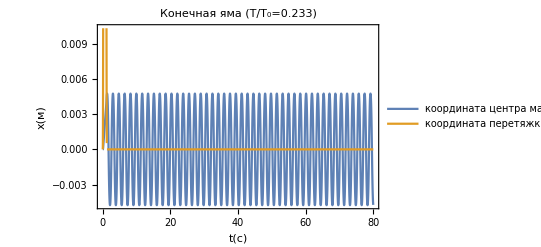

0.00476182

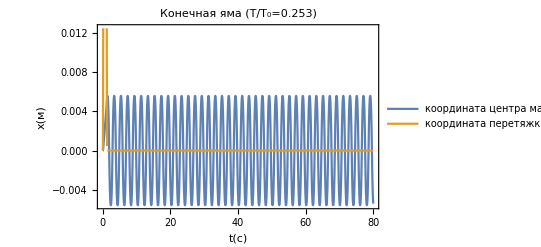

0.00557227

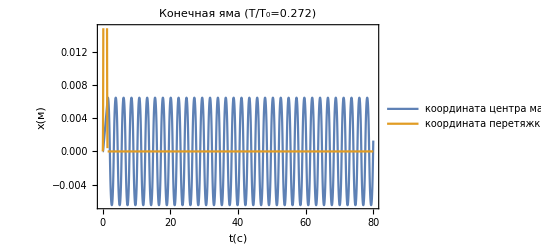

0.00646951

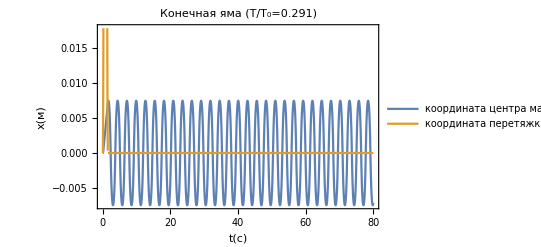

0.00745973

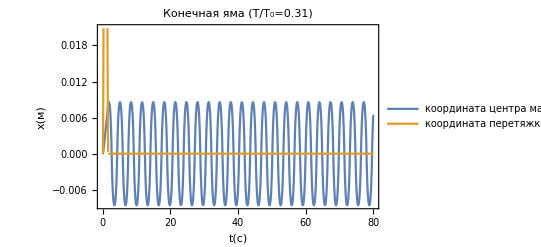

0.00856621

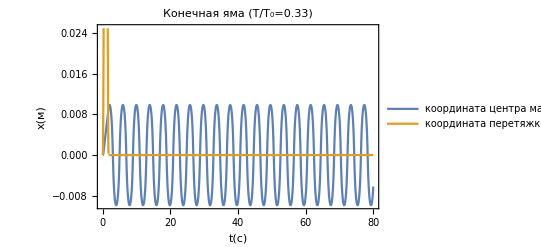

0.00982151

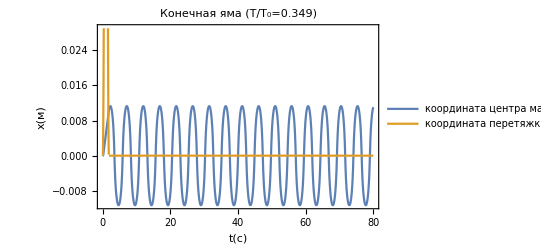

0.0112772

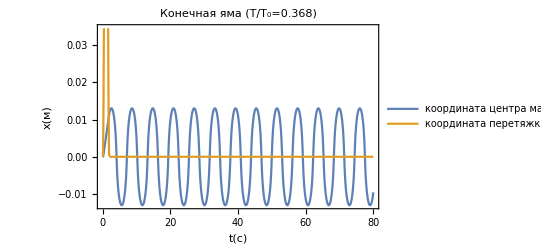

0.0130244

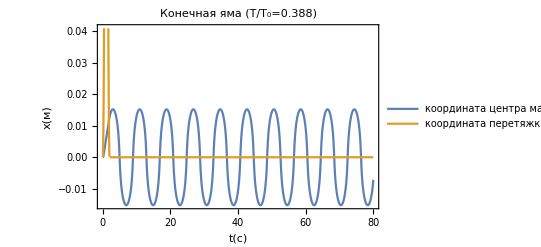

0.0152242

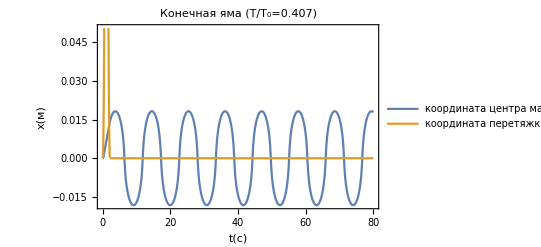

0.0182004

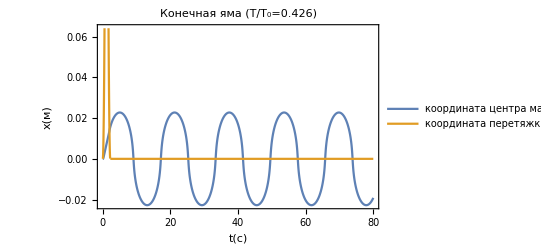

0.0227482

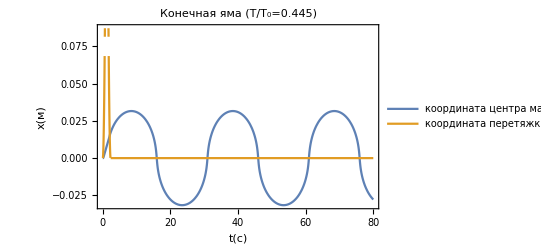

0.0315915

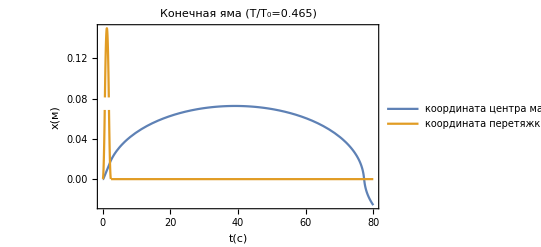

0.0202564

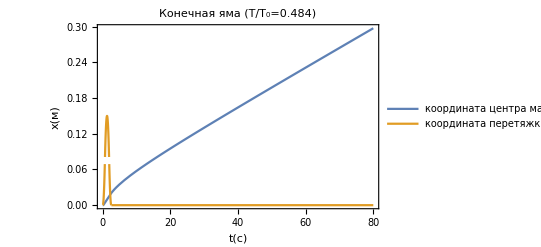

0.0329288

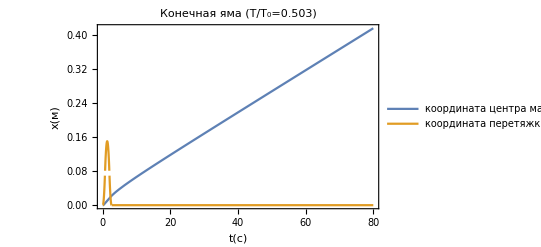

0.0492033

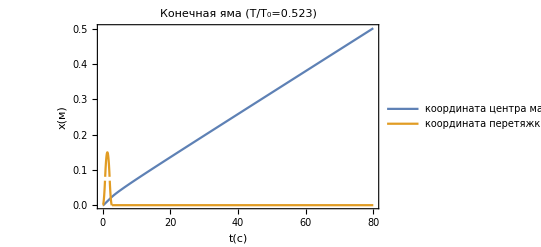

0.0608084

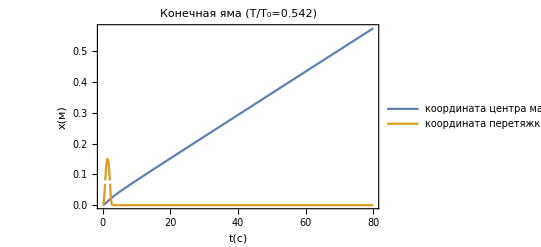

0.0702169

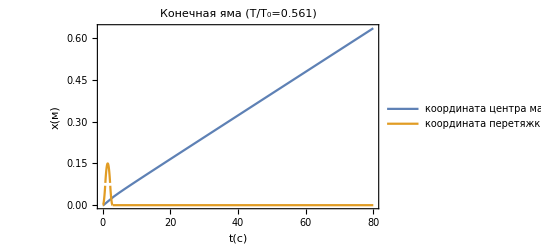

0.0783265

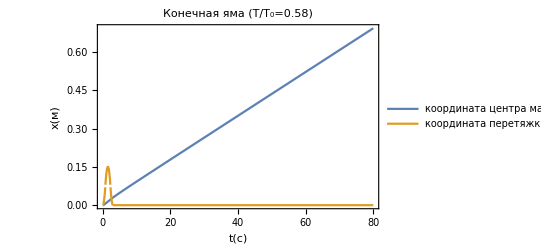

0.0855886

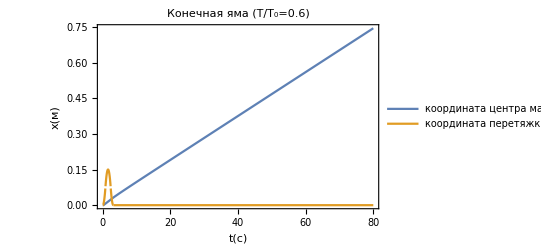

0.0922688

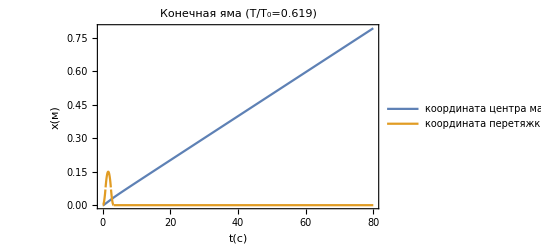

0.0985379

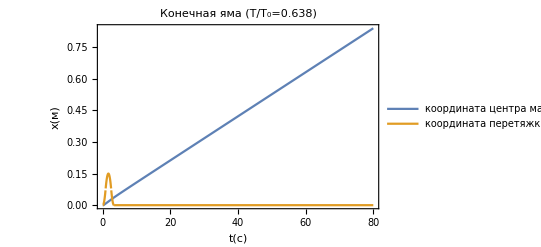

0.104515

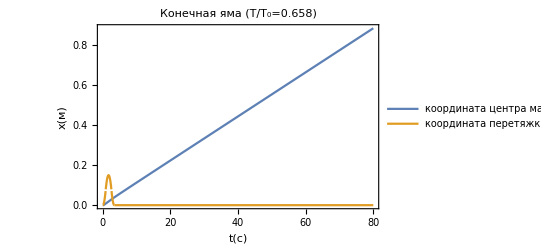

0.110284

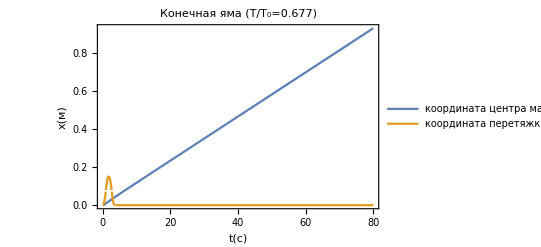

0.115911

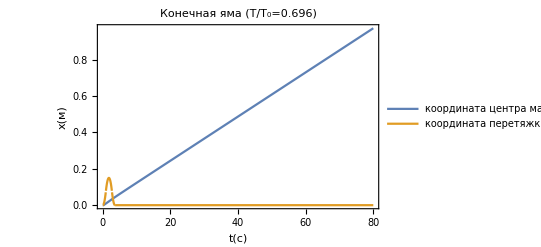

0.121445

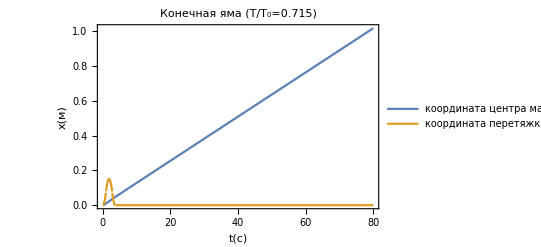

0.126926

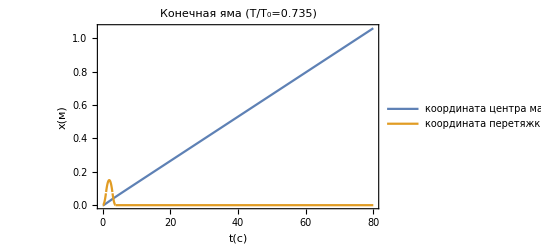

0.132388

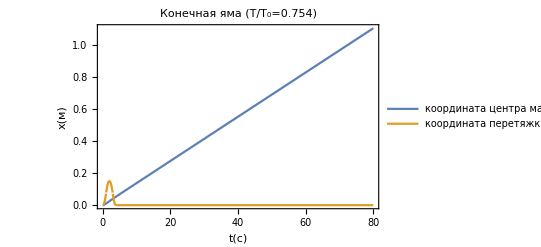

0.137857

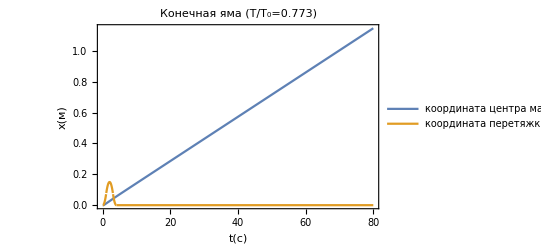

0.14336

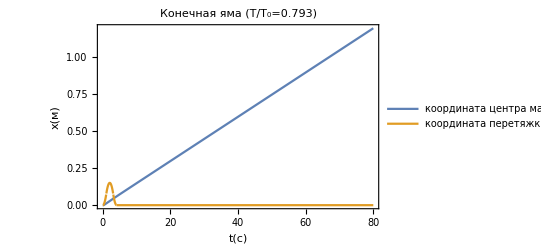

0.148918

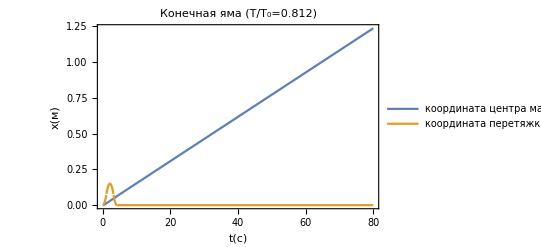

0.154553

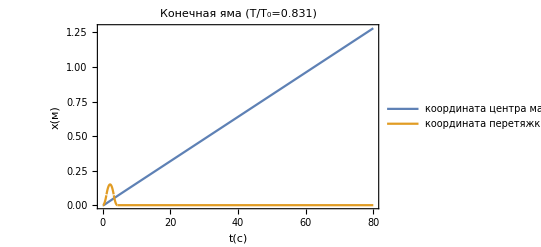

0.160285

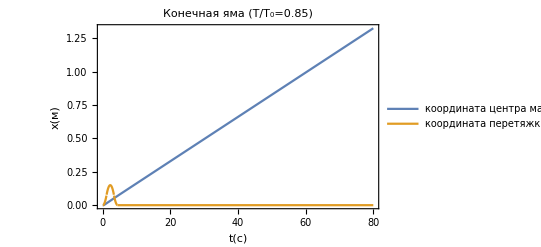

0.166135

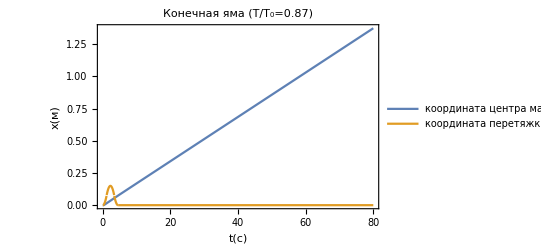

0.172125

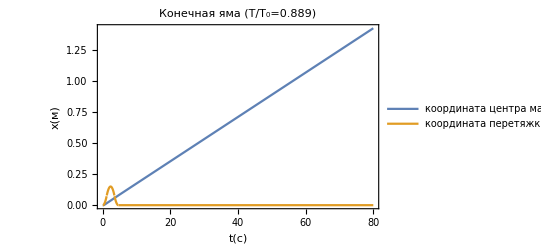

0.178279

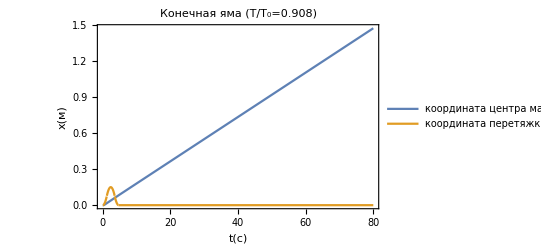

0.184628

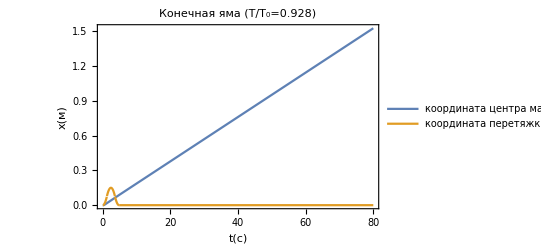

0.191214

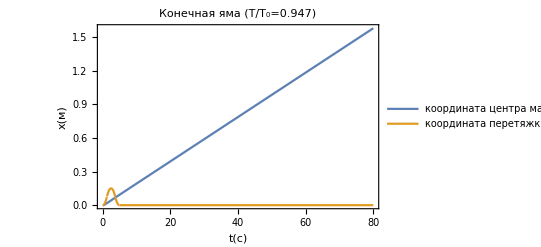

0.19811

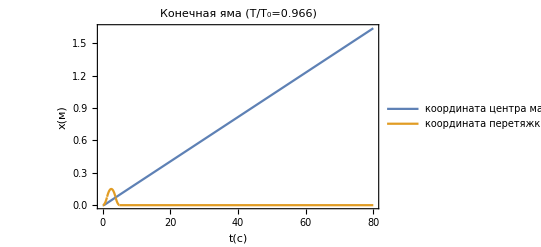

0.205481

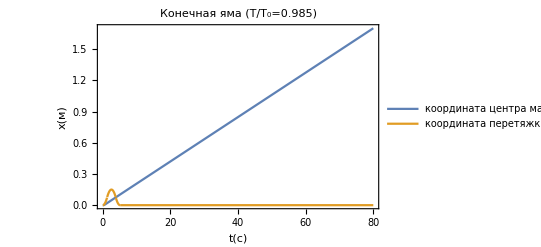

0.213618

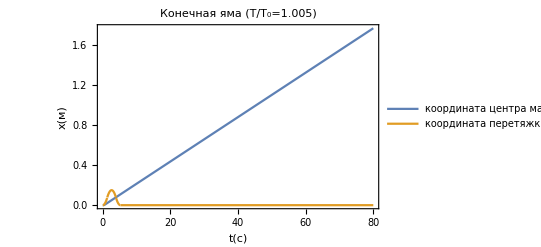

0.222102

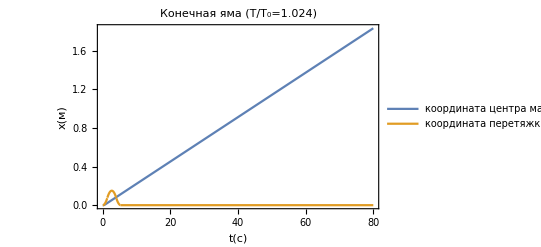

0.230418

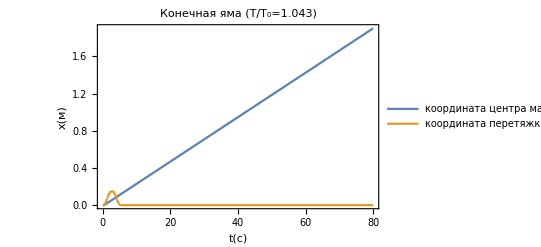

0.238867

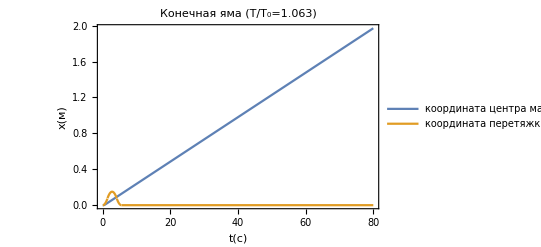

0.247656

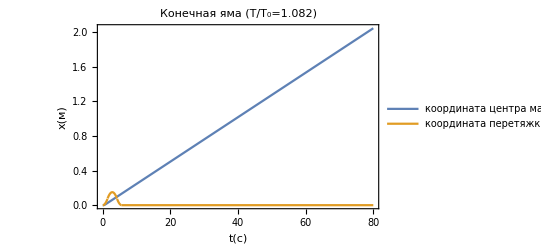

0.256901

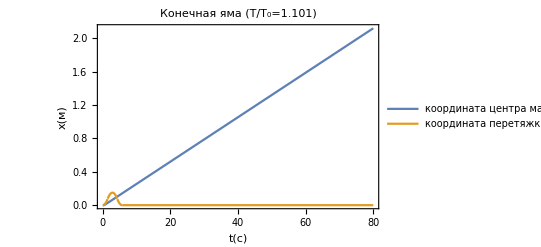

0.2667

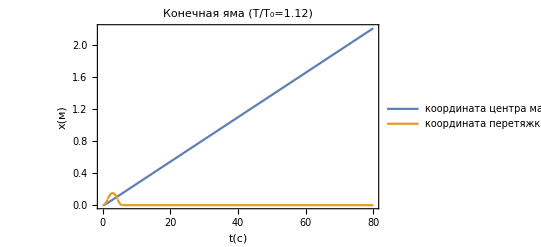

0.277148

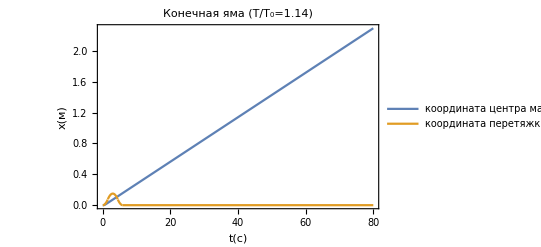

0.288362

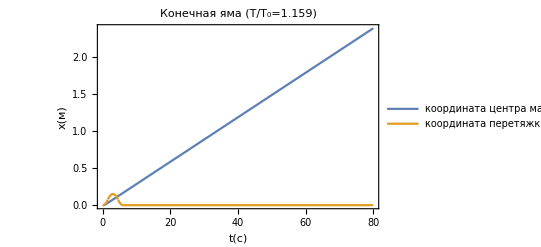

0.300479

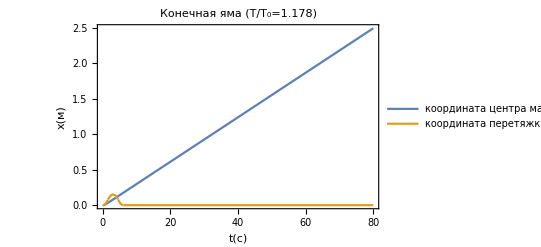

0.313675

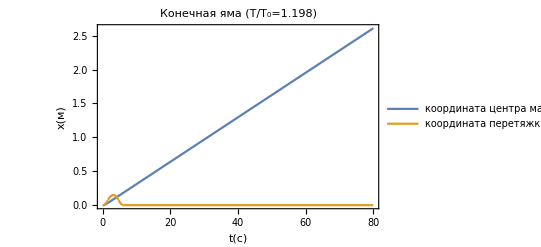

0.328177

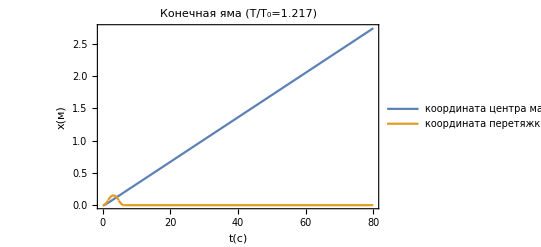

0.344288

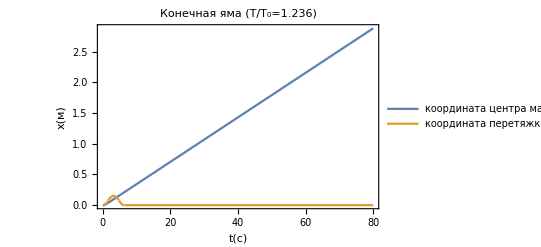

0.362428

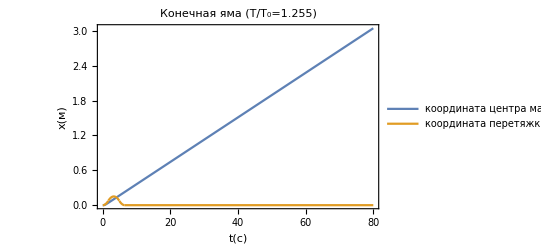

0.383202

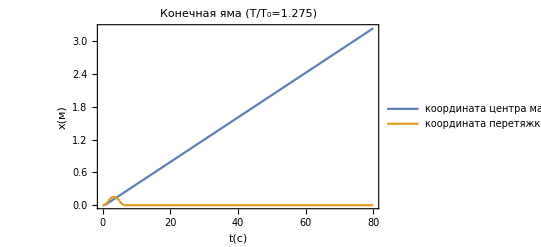

0.407527

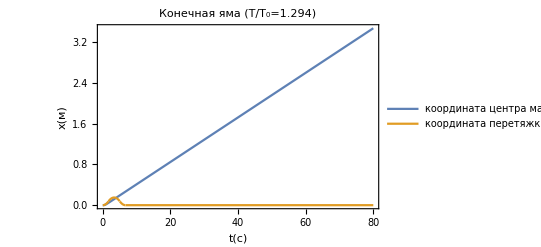

0.436881

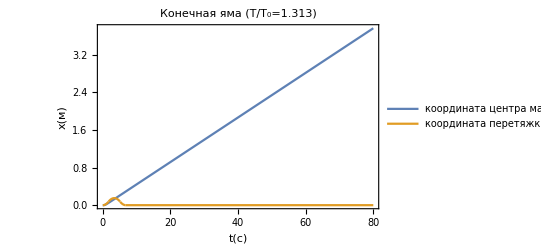

0.473908

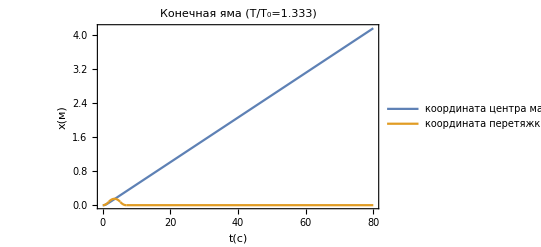

0.524013

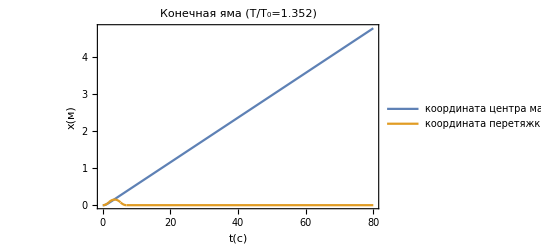

0.601087

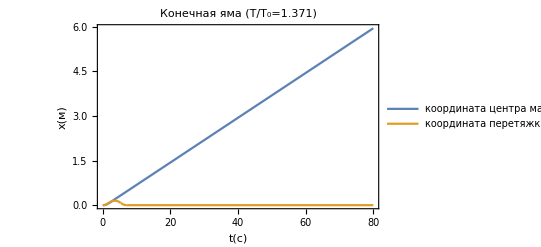

0.75317

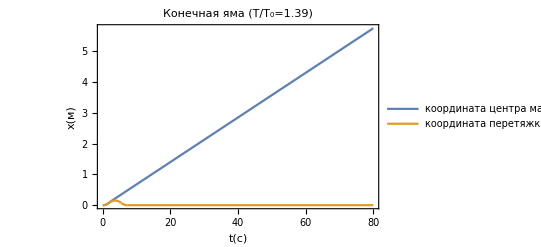

0.723882

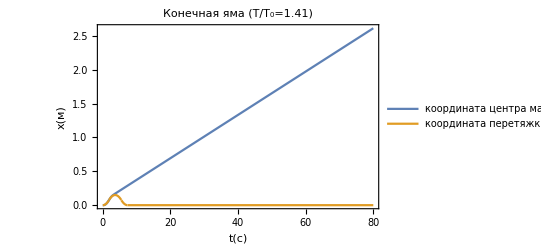

0.319833

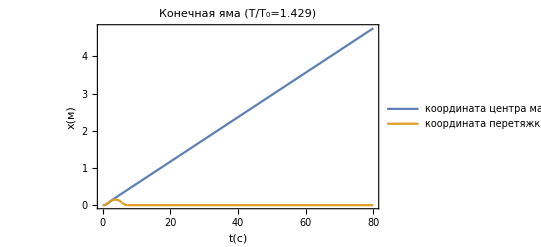

0.59718

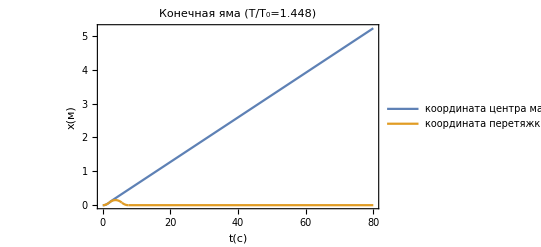

0.657717

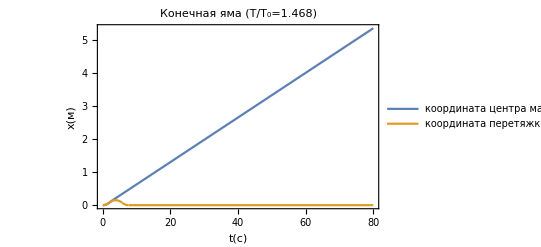

0.675501

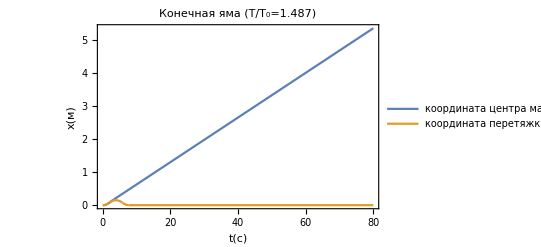

0.675547

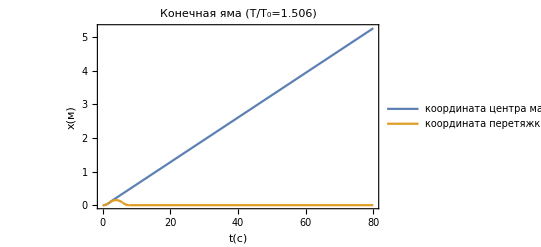

0.6648

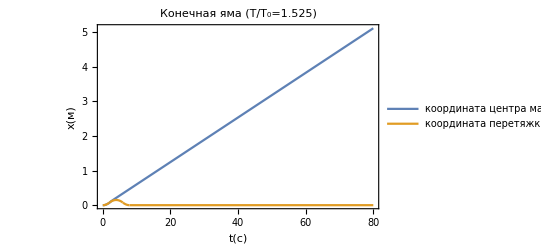

0.645111

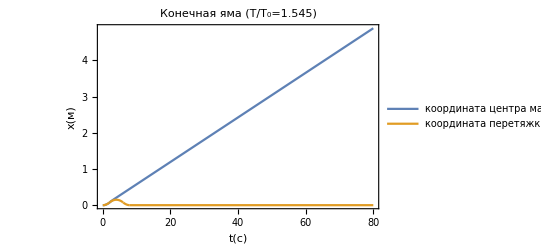

0.615989

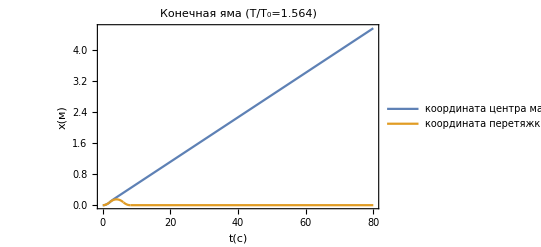

0.57481

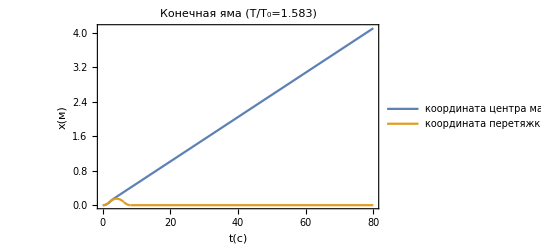

0.514711

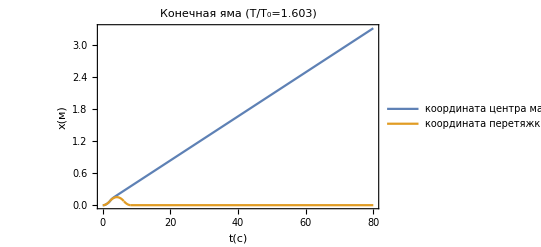

0.412362

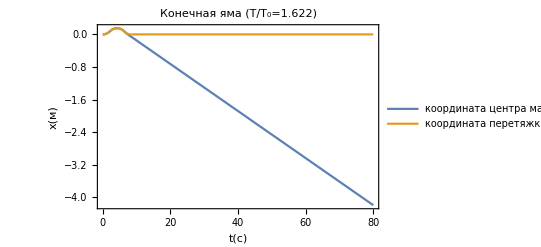

0.577291

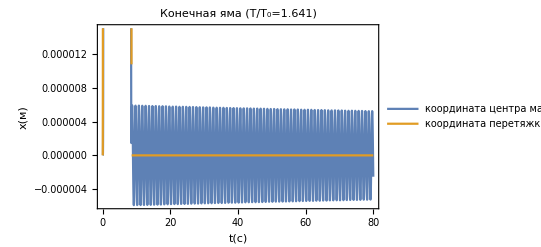

5.13706×10^-6

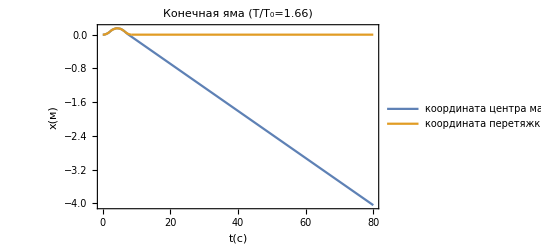

0.558335

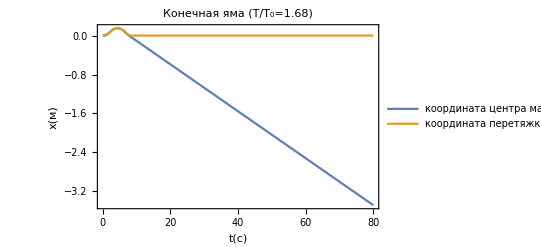

0.482311

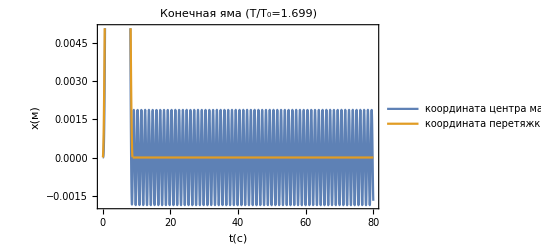

0.00187126

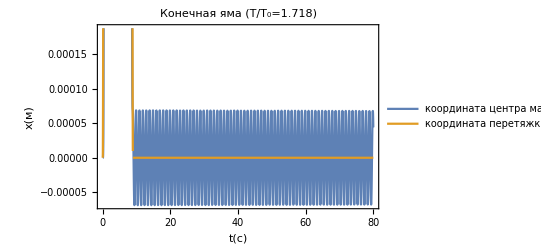

0.0000658896

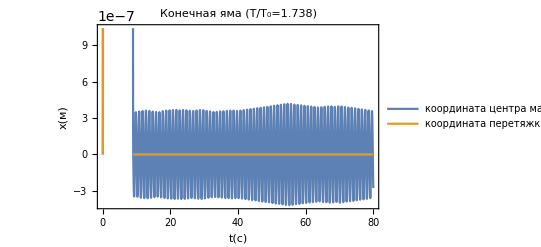

3.60777×10^-7

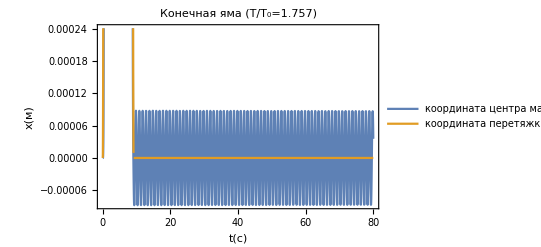

0.0000864322

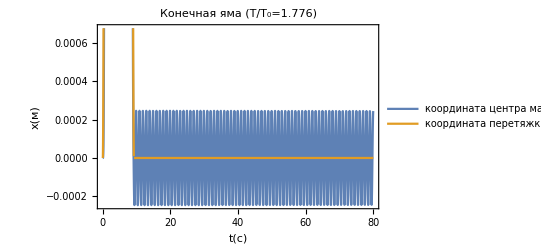

0.000244043

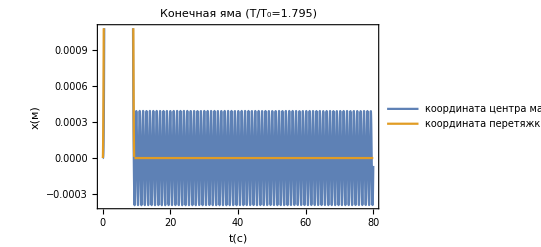

0.000391716

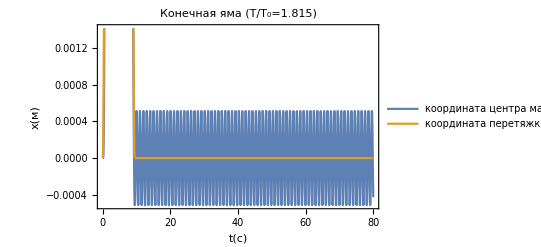

0.000513327

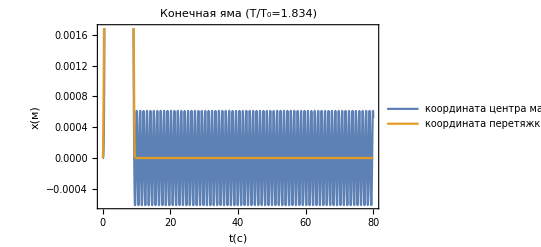

0.000611845

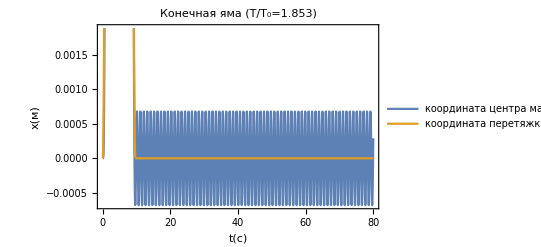

0.000680276

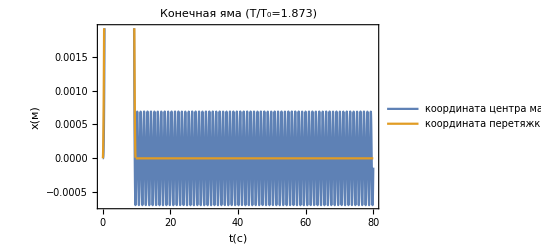

0.000690525

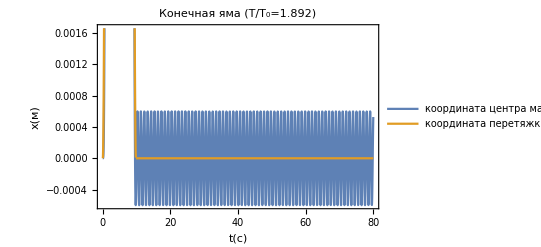

0.000598176

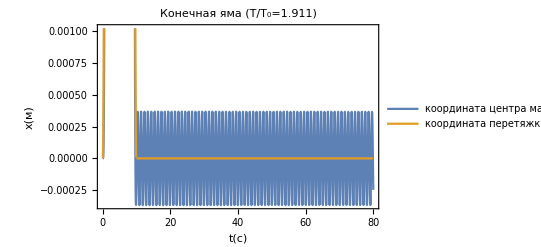

0.000366183

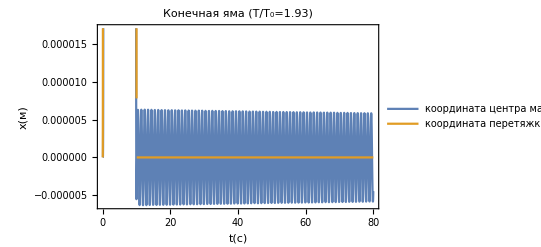

5.81254×10^-6

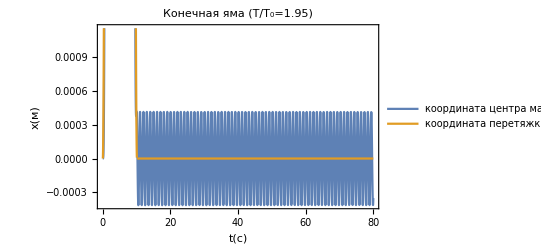

0.00041281

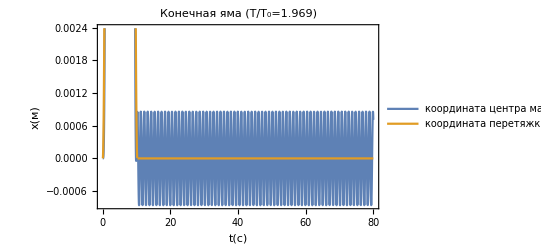

0.000858358

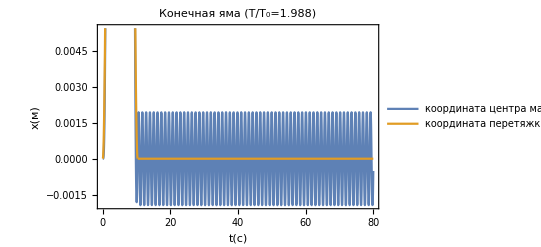

0.00193809

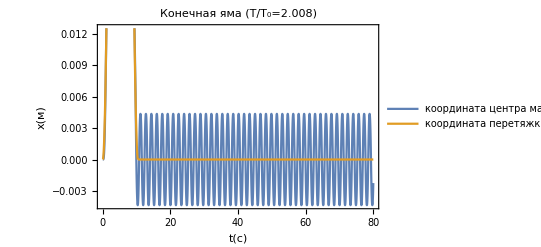

0.00435211

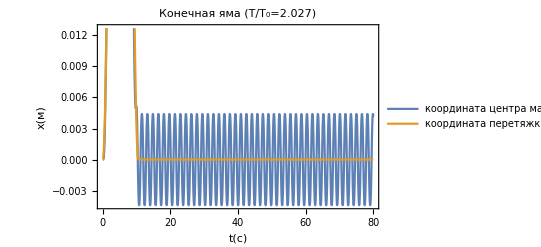

0.00440044

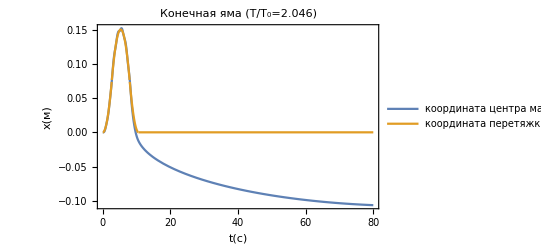

0.000656328

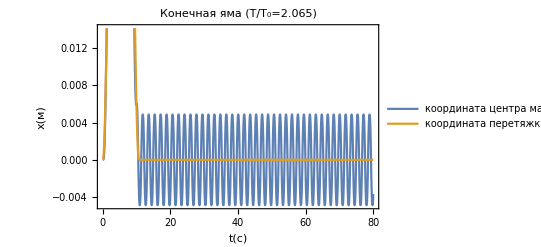

0.00487454

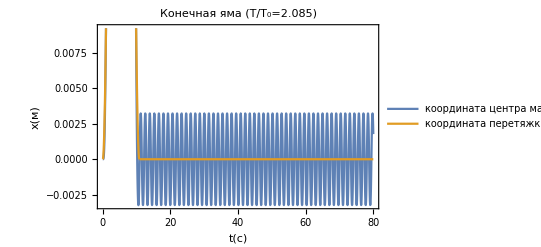

0.0032389

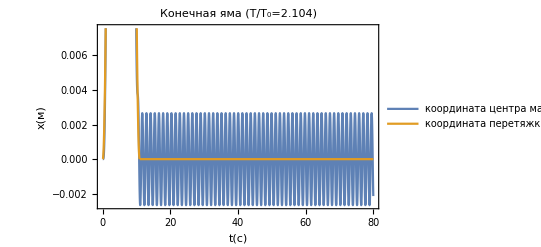

0.00265401

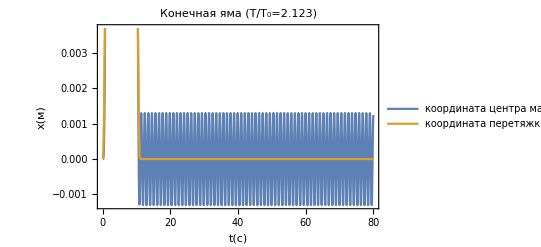

0.00130229

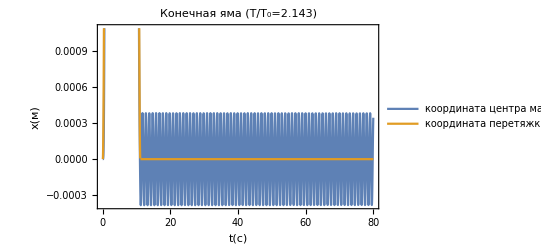

0.000380607

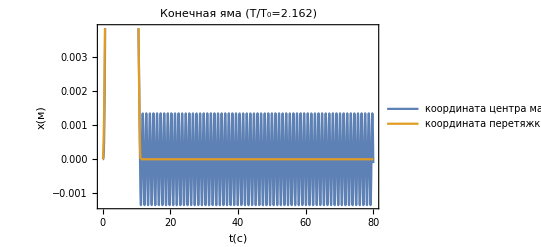

0.00135272

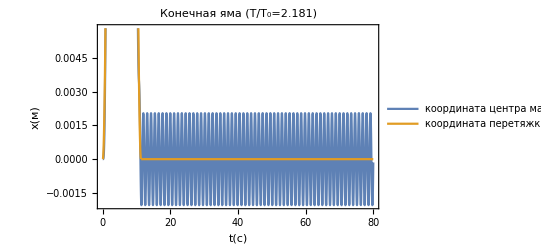

0.00204063

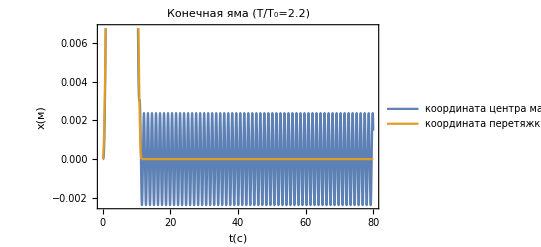

0.00237437

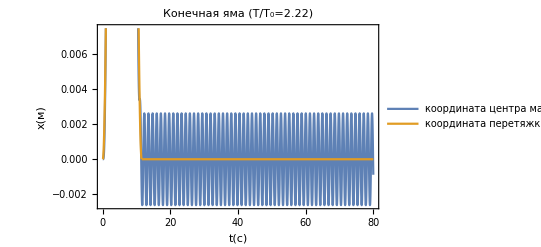

0.00260515

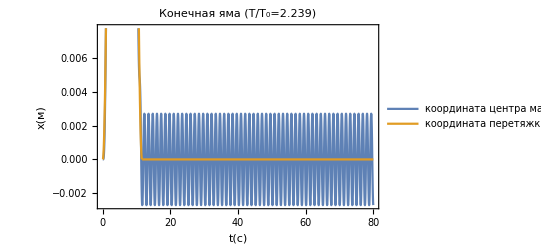

0.00271012

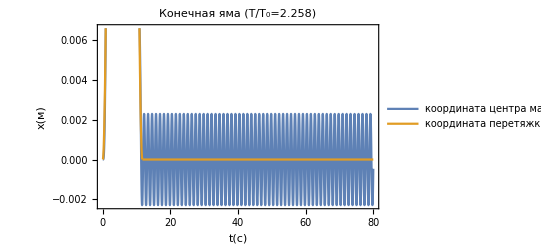

0.00229199

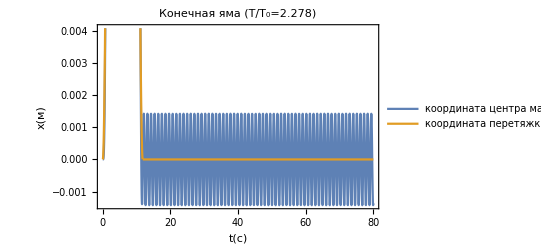

0.00142648

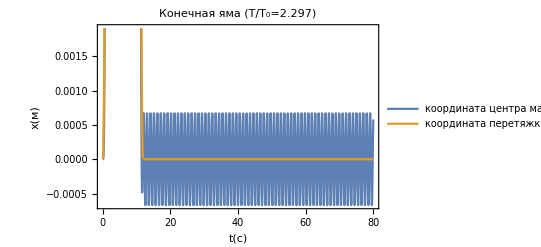

0.000668685

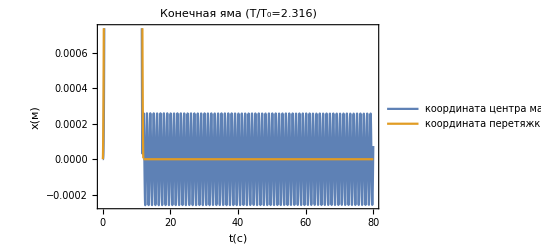

0.000256734

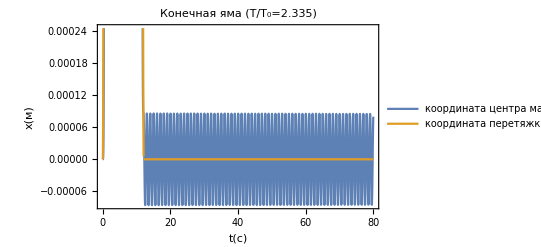

0.0000824133

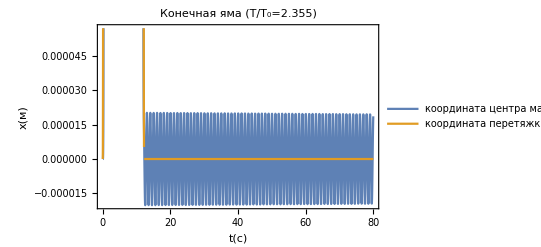

0.0000185757

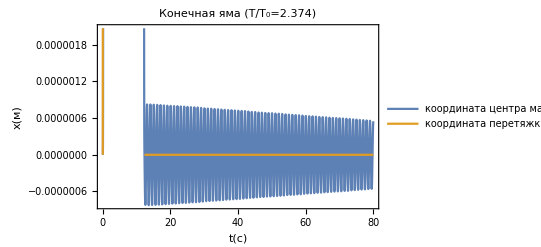

5.48427×10^-7

-Graphics-

1.04947×10^-6

-Graphics-

2.86334×10^-6

-Graphics-

0.0000329678

-Graphics-

0.000101699

-Graphics-

0.000210856

-Graphics-

0.000347232

-Graphics-

0.000503013

-Graphics-

0.00066522

-Graphics-

0.000824129

-Graphics-

0.000970811

-Graphics-

0.00109667

-Graphics-

0.00119601

-Graphics-

0.00126931

-Graphics-

0.00133394

-Graphics-

0.00142319

-Graphics-

0.0015468

-Graphics-

0.00163167

-Graphics-

0.00155505

-Graphics-

0.00125929

-Graphics-

0.000793895

-Graphics-

0.000277982

-Graphics-

0.00018431

-Graphics-

0.000580162

-Graphics-

0.00090749

-Graphics-

0.00117125

-Graphics-

0.00136689

-Graphics-

0.00148369

-Graphics-

0.00150167

-Graphics-

0.00140461

-Graphics-

0.00119329

-Graphics-

0.00090559

-Graphics-

0.00061151

-Graphics-

0.000367551

-Graphics-

0.000194282

-Graphics-

0.0000910506

-Graphics-

0.0000335202

-Graphics-

7.09784×10^-6

-Graphics-

3.55435×10^-7

-Graphics-

8.77685×10^-8

-Graphics-

4.64275×10^-6

-Graphics-

0.0000244067

-Graphics-

0.0000676383

-Graphics-

0.000134198

-Graphics-

0.000218212

-Graphics-

0.00032206

-Graphics-

0.000432024

-Graphics-

0.000542007

-Graphics-

0.000647912

-Graphics-

0.000747762

-Graphics-

0.00083956

-Graphics-

0.000921276

-Graphics-

0.000986286

-Graphics-

0.00102047

-Graphics-

0.0010029

-Graphics-

0.000921237

-Graphics-

0.00076769

-Graphics-

0.000553302

-Graphics-

0.000303263

-Graphics-

0.0000459227

-Graphics-

0.00019194

-Graphics-

0.000409137

-Graphics-

0.000594

-Graphics-

0.000742655

-Graphics-

0.000850034

-Graphics-

0.000910371

-Graphics-

0.000918356

-Graphics-

0.000870704

-Graphics-

0.000772144

-Graphics-

0.00063707

-Graphics-

0.000485612

-Graphics-

0.000340337

-Graphics-

0.000217967

-Graphics-

0.000122601

-Graphics-

0.0000615426

-Graphics-

0.0000248705

-Graphics-

6.05346×10^-6

-Graphics-

3.66912×10^-7

-Graphics-

8.59307×10^-8

-Graphics-

1.76231×10^-6

-Graphics-

0.000011624

-Graphics-

0.0000363371

-Graphics-

0.0000750733

-Graphics-

0.000127907

-Graphics-

0.000198704

-Graphics-

0.000277974

-Graphics-

0.000359621

-Graphics-

0.000441095

-Graphics-

0.000517769

-Graphics-

0.000586343

-Graphics-

0.000641317

-Graphics-

0.000676412

-Graphics-

0.00068357

-Graphics-

0.000655704

-Graphics-

0.000588768

-Graphics-

0.000483023

-Graphics-

0.000345553

-Graphics-

0.000189124

-Graphics-

0.0000261114

-Graphics-

0.000125769

-Graphics-

0.000273486

-Graphics-

0.000398337

-Graphics-

0.000498762

-Graphics-

0.000570961

-Graphics-

0.000611715

-Graphics-

0.000619063

-Graphics-

0.000592732

-Graphics-

0.000536154

-Graphics-

0.000456613

-Graphics-

0.000364601

-Graphics-

0.000271312

-Graphics-

0.000186849

-Graphics-

0.000117129

-Graphics-

0.0000659461

-Graphics-

0.0000302643

-Graphics-

0.0000107993

-Graphics-

1.89768×10^-6

-Graphics-

8.1917×10^-8

-Graphics-

9.88785×10^-8

-Graphics-

2.89649×10^-6

-Graphics-

0.0000127422

-Graphics-

0.0000336609

-Graphics-

0.0000636197

-Graphics-

0.000109468

-Graphics-

0.000162563

-Graphics-

0.000221568

-Graphics-

0.000282514

-Graphics-

0.000342759

-Graphics-

0.000398333

-Graphics-

0.000443945

-Graphics-

0.000475256

-Graphics-

0.000487671

-Graphics-

0.000477077

-Graphics-

0.000440586

-Graphics-

0.000377539

-Graphics-

0.000291025

-Graphics-

0.000188424

-Graphics-

0.0000764367

-Graphics-

0.0000357514

-Graphics-

0.000143382

-Graphics-

0.000240526

-Graphics-

0.000323883

-Graphics-

0.000386869

-Graphics-

0.000427686

-Graphics-

0.00044532

-Graphics-

0.0004393

-Graphics-

0.000411185

-Graphics-

0.000364807

-Graphics-

0.000304329

-Graphics-

0.000241825

-Graphics-

0.000178803

-Graphics-

0.000122208

-Graphics-

0.0000738269

-Graphics-

0.0000414395

-Graphics-

0.0000186907

-Graphics-

6.01635×10^-6

-Graphics-

9.17372×10^-7

-Graphics-

9.11807×10^-8

-Graphics-

2.98993×10^-7

-Graphics-

2.92544×10^-6

-Graphics-

0.0000115705

-Graphics-

0.0000281334

-Graphics-

0.0000533572

-Graphics-

0.0000883584

-Graphics-

0.00012738

-Graphics-

0.000170007

-Graphics-

0.000219742

-Graphics-

0.000266373

-Graphics-

0.000308008

-Graphics-

0.000340179

-Graphics-

0.000359632

-Graphics-

0.000363413

-Graphics-

0.000348859

-Graphics-

0.000315467

-Graphics-

0.000263413

-Graphics-

0.000192882

-Graphics-

0.000114298

-Graphics-

0.0000335346

-Graphics-

0.0000490862

-Graphics-

0.000129607

-Graphics-

0.000200054

-Graphics-

0.000258105

-Graphics-

0.000301095

-Graphics-

0.000327095

-Graphics-

0.000335482

-Graphics-

0.000326807

-Graphics-

0.000302722

-Graphics-

0.000266202

-Graphics-

0.000221048

-Graphics-

0.000171212

-Graphics-

0.000125541

-Graphics-

0.0000874629

-Graphics-

0.0000534559

-Graphics-

0.0000288138

-Graphics-

0.0000127471

-Graphics-

3.88119×10^-6

-Graphics-

5.23208×10^-7

-Graphics-

9.52229×10^-8

-Graphics-

3.98644×10^-7

-Graphics-

2.63342×10^-6

-Graphics-

9.9938×10^-6

-Graphics-

0.0000230742

-Graphics-

0.0000437767

-Graphics-

0.0000708938

-Graphics-

0.000100735

-Graphics-

0.00014002

-Graphics-

0.000176968

-Graphics-

0.00021097

-Graphics-

0.000240398

-Graphics-

0.000266879

-Graphics-

0.000279737

-Graphics-

0.00028048

-Graphics-

0.000265297

-Graphics-

0.000238236

-Graphics-

0.000196104

-Graphics-

0.000142889

-Graphics-

0.0000797633

-Graphics-

0.0000155457

-Graphics-

0.0000484385

-Graphics-

0.00011

-Graphics-

0.000162528

-Graphics-

0.000202888

-Graphics-

0.00023863

-Graphics-

0.00025727

-Graphics-

0.000258759

-Graphics-

0.000253045

-Graphics-

0.000232673

-Graphics-

0.000199461

-Graphics-

0.000168988

-Graphics-

0.000133222

-Graphics-

0.0000953811

-Graphics-

0.0000656924

-Graphics-

0.0000406417

-Graphics-

0.0000213713

-Graphics-

9.53275×10^-6

-Graphics-

2.69585×10^-6

-Graphics-

3.69316×10^-7

-Graphics-

9.49094×10^-8

-Graphics-

3.04957×10^-7

-Graphics-

2.30133×10^-6

-Graphics-

8.45921×10^-6

-Graphics-

0.0000189372

-Graphics-

0.0000361545

-Graphics-

0.0000573716

-Graphics-

0.0000834756

-Graphics-

0.000113698

-Graphics-

0.000139977

-Graphics-

0.000171319

-Graphics-

0.000196052

-Graphics-

0.000210494

-Graphics-

0.000224033

-Graphics-

0.000220414

-Graphics-

0.000210753

-Graphics-

0.000185534

-Graphics-

0.00014898

-Graphics-

0.00010886

-Graphics-

0.0000592135

-Graphics-

7.17972×10^-6

-Graphics-

0.0000438411

-Graphics-

0.000092092

-Graphics-

0.000130754

-Graphics-

0.000169543

-Graphics-

0.000193561

-Graphics-

0.000203575

-Graphics-

0.000209926

-Graphics-

0.000198821

-Graphics-

0.00018491

-Graphics-

0.000161908

-Graphics-

0.00012921

-Graphics-

0.00010488

-Graphics-

0.0000763117

-Graphics-

0.0000513818

-Graphics-

0.0000320244

-Graphics-

0.0000166891

-Graphics-

7.3095×10^-6

-Graphics-

2.03174×10^-6

-Graphics-

3.46143×10^-7

```mathematica
α=160*2.61*10^-39;
x0=0;
x1 = 0.001;
x2 = 0.01
x3 = 100
P=20;
ω0=40*10^-6;
λ=1064*10^-9;
mTh=169*1.66*10^-27;
k = 1.38 * 10^-23;
l=0.15;
T = 20 * 10^-6;
xrel=(π ω0^2)/λ;
F[x_]=-D[(-2α P)/(π ω0^2)(1-(x/xrel)^2),x]; (*после разложения в тейлора*)
F[x_]=-D[(-2α P)/(π ω0^2(1+(x/xrel)^2)),x]; 
νx=1/(2π)√((2(2α P)/(π ω0^2))/(mTh xrel^2));
T0=1/νx;
v0 =√((k*T)/mTh);

(*Plot[(-2α P)/(π ω0^2(1+(x/xrel)^2)), {x,-0.05,0.05},FrameLabel->{"x(м)", "u(Дж)"} ,Frame->True, PlotRange->All]
Plot[(-2α P)/(π ω0^2)(1-(x/xrel)^2), {x,-0.05,0.05},FrameLabel->{"x(м)", "u(Дж)"} ,Frame->True, PlotRange->All]

Plot[F[x],{x,-0.5,0.5}, Frame->True,FrameLabel->{"x(м)", "F(Н)"}, PlotRange->All]*)
Aampl0={};
Aampl1={};
Aampl2={};
Aampl3={};
Clear[i];

For[i=0.01 T0,i≤40 T0,i=i+ T0,a=(16 l)/i^2;
(*Print[i/T0];*)
(*aa[t_]=Boole[0≤t≤i/4]-Boole[i/4≤t≤i/4+i/2]+Boole[i/4+i/2≤t≤i];*)
aa[t_] = BlackmanHarrisWindow[t] 
(*Print[Plot[aa[t],{t,0,i}, Frame->True,FrameLabel->{"t(c)","a(a_0)"}]];*)
sp=Quiet[DSolve[{x''[t]==a*aa[t],x[0]==x0,x'[0]==0},x[t],t]];
xp[t_]=Evaluate[x[t]/.sp][[1]];
vsp[t_]=Evaluate[D[xp[t],t]];
(*Print[Plot[vsp[t T0],{t,0,i/T0}, Frame->True,FrameLabel->{"t(c)","v(м/с)"}]];*)
(*Print[Plot[xp[t T0],{t,0,i/T0},Frame->True,FrameLabel->{"t(c)","x(м)"}]];*)
cc0[t_]=Evaluate[y[t]/.NDSolve[{F[y[t]-xp[t]]==mTh y''[t],y[0]==x0,y'[0]== 0},y[t],{t,0,100 T0}]];
cc1[t_]=Evaluate[y[t]/.NDSolve[{F[y[t]-xp[t]]==mTh y''[t],y[0]==x0,y'[0]== v0},y[t],{t,0,100 T0}]];
cc2[t_]=Evaluate[y[t]/.NDSolve[{F[y[t]-xp[t]]==mTh y''[t],y[0]==x0,y'[0]== 2*v0},y[t],{t,0,100 T0}]];
cc3[t_]=Evaluate[y[t]/.NDSolve[{F[y[t]-xp[t]]==mTh y''[t],y[0]==x0,y'[0]== 3*v0},y[t],{t,0,100 T0}]];
ampl0=(Max[Table[cc0[i],{i,80 T0,100 T0,T0/10}]]-Min[Table[cc0[i],{i,80 T0,100 T0,T0/10}]])/2;
ampl1=(Max[Table[cc1[i],{i,80 T0,100 T0,T0/10}]]-Min[Table[cc1[i],{i,80 T0,100 T0,T0/10}]])/2;
ampl2=(Max[Table[cc2[i],{i,80 T0,100 T0,T0/10}]]-Min[Table[cc2[i],{i,80 T0,100 T0,T0/10}]])/2;
ampl3=(Max[Table[cc3[i],{i,80 T0,100 T0,T0/10}]]-Min[Table[cc3[i],{i,80 T0,100 T0,T0/10}]])/2;

Print[Plot[{cc0[t T0],xp[t T0]},{t,0,80}, Frame->True,FrameLabel->{"t(c)","x(м)"},PlotLegends->{"координата центра масс атомов тулия", "координата перетяжки"}, PlotLabel->"Конечная яма (T/T_0=" <> ToString[Round[i, 0.001]] <> ")"]];
Print[ampl0];
Aampl0=AppendTo[Aampl0,{i/T0,ampl0}];
Aampl1=AppendTo[Aampl1,{i/T0,ampl1}];
Aampl2=AppendTo[Aampl2,{i/T0,ampl2}];
Aampl3=AppendTo[Aampl3,{i/T0,ampl3}];
]
```

```mathematica
ListLinePlot[{Aampl0, Aampl1, Aampl2, Aampl3}, Frame->True, FrameLabel->{"T/T_0", "A(m)"},PlotLegends->Table["v/v_0="<>ToString[i],{i,0,3,1}], PlotRange->{All, {0, 0.005}}, PlotLabel->"Конечная яма"]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Abs[FourierTransform[cc[ttt],ttt,ω]]/.ω-> 2π νx;
δ=T0/100;
data=Table[{t,cc[t][[1]]},{t,0,10T0,δ}];
ff=Abs[Fourier[data[[;;,2]]]];
ff=ff[[;;Round[Length[ff]/2]]];
n=Length[data];
xxx=Table[i,{i,0,n-1}];
fff=Take[Transpose[{xxx 1/(n*δ),Abs[Fourier[data[[;;,2]]]]}],Round[n/2]];
Show[ListLinePlot[fff[[10;;500]],PlotRange->All,PlotMarkers->Automatic],Graphics[Line[{{νx,0},{νx,10}}]]]
```

-Graphics-

```mathematica
u[x] = (-2α P)/(π ω0^2(1+(x/xrel)^2))  + (2α P)/(π ω0^2); (*Сделал так, что u(0)=0*)
k = 1.38 10^(-23);
T = 10 * 10^(-6);
Subscript[N, 0]=1000000;
pl[x] = Subscript[N, 0] Exp[-u[x]/(k*T) ];

Plot[pl[x], {x, 0, 5 10^(-3)}]
```

```mathematica
α=160*2.61*10^-39;

x0=0;

x1=0.001;

x2=0.005

x3=0.008

P=20;

ω0=40*10^-6;

λ=1064*10^-9;

mTh=169*1.66*10^-27;

k=1.38*10^-23;

l=0.15;

T=20*10^-6;

xrel=(π ω0^2)/λ;

F[x_]=-D[(-2 α P)/(π ω0^2) (1-(x/xrel)^2),x];

νx=1/(2 π) Sqrt[(2 (2 α P)/(π ω0^2))/(mTh xrel^2)];

T0=1/νx;

v0=Sqrt[(k*T)/mTh];






Aampl0={};

Aampl1={};

Aampl2={};

Aampl3={};

Clear[i];




For[i=0.01 T0,i≤40 T0,i=i+0.1 T0,a=(16 l)/i^2;
aa[t_]=Boole[0≤t≤i/4]-Boole[i/4≤t≤i/4+i/2]+Boole[i/4+i/2≤t≤i];
sp=Quiet[DSolve[{x''[t]==a*aa[t],x[0]==0,x'[0]==0},x[t],t]];
xp[t_]=Evaluate[x[t]/.sp][[1]];
vsp[t_]=Evaluate[D[xp[t],t]];
cc0[t_]=Evaluate[y[t]/.NDSolve[{F[y[t]-xp[t]]==mTh y''[t],y[0]==x0,y'[0]==0},y[t],{t,0,100 T0}]];
cc1[t_]=Evaluate[y[t]/.NDSolve[{F[y[t]-xp[t]]==mTh y''[t],y[0]==x1,y'[0]==0},y[t],{t,0,100 T0}]];
cc2[t_]=Evaluate[y[t]/.NDSolve[{F[y[t]-xp[t]]==mTh y''[t],y[0]==x2,y'[0]==0},y[t],{t,0,100 T0}]];
cc3[t_]=Evaluate[y[t]/.NDSolve[{F[y[t]-xp[t]]==mTh y''[t],y[0]==x3,y'[0]==0},y[t],{t,0,100 T0}]];
ampl0=(Max[Table[cc0[i],{i,80 T0,100 T0,T0/10}]]-Min[Table[cc0[i],{i,80 T0,100 T0,T0/10}]])/2;
ampl1=(Max[Table[cc1[i],{i,80 T0,100 T0,T0/10}]]-Min[Table[cc1[i],{i,80 T0,100 T0,T0/10}]])/2;
ampl2=(Max[Table[cc2[i],{i,80 T0,100 T0,T0/10}]]-Min[Table[cc2[i],{i,80 T0,100 T0,T0/10}]])/2;
ampl3=(Max[Table[cc3[i],{i,80 T0,100 T0,T0/10}]]-Min[Table[cc3[i],{i,80 T0,100 T0,T0/10}]])/2;
Aampl0=AppendTo[Aampl0,{i/T0,ampl0}];
Aampl1=AppendTo[Aampl1,{i/T0,ampl1}];
Aampl2=AppendTo[Aampl2,{i/T0,ampl2}];
Aampl3=AppendTo[Aampl3,{i/T0,ampl3}];]




ListLinePlot[{Aampl0,Aampl1,Aampl2,Aampl3},Frame->True,FrameLabel->{"T/\!\(\*SubscriptBox[\(T\), \(0\)]\)","A(m)"},PlotLegends->{"0","0.001\!\(\*SubscriptBox[\(x\), \(0\)]\)","0.01\!\(\*SubscriptBox[\(x\), \(0\)]\)","0.02\!\(\*SubscriptBox[\(x\), \(0\)]\)"},PlotRange->{All,{0,0.05}}]
```

0.005

0.008

-Graphics-

```mathematica
ListLinePlot[{Aampl0,Aampl1,Aampl2,Aampl3},Frame->True,FrameLabel->{"T/\!\(\*SubscriptBox[\(T\), \(0\)]\)","A(m)"},PlotLegends->{"x_0=0","x_0=0.002 m","x_0=0.005 m","x_0=0.008 m"},PlotRange->{All,{0,0.02}}, PlotLabel->"Бесконечна яма"]
```

-Graphics-

```mathematica
α=160*2.61*10^-39;

x0=0;

x1=0.001;

x2=0.005

x3=0.008

P=20;

ω0=40*10^-6;

λ=1064*10^-9;

mTh=169*1.66*10^-27;

k=1.38*10^-23;

l=0.15;

T=20*10^-6;

xrel=(π ω0^2)/λ;

F[x_]=-D[(-2 α P)/(π ω0^2 (1+(x/xrel)^2)),x];

νx=1/(2 π) Sqrt[(2 (2 α P)/(π ω0^2))/(mTh xrel^2)];

T0=1/νx;

v0=Sqrt[(k*T)/mTh];






Aampl0={};

Aampl1={};

Aampl2={};

Aampl3={};

Clear[i];




For[i=0.01 T0,i≤40 T0,i=i+0.1 T0,a=(16 l)/i^2;
aa[t_]=Boole[0≤t≤i/4]-Boole[i/4≤t≤i/4+i/2]+Boole[i/4+i/2≤t≤i];
sp=Quiet[DSolve[{x''[t]==a*aa[t],x[0]==0,x'[0]==0},x[t],t]];
xp[t_]=Evaluate[x[t]/.sp][[1]];
vsp[t_]=Evaluate[D[xp[t],t]];
cc0[t_]=Evaluate[y[t]/.NDSolve[{F[y[t]-xp[t]]==mTh y''[t],y[0]==x0,y'[0]==0},y[t],{t,0,100 T0}]];
cc1[t_]=Evaluate[y[t]/.NDSolve[{F[y[t]-xp[t]]==mTh y''[t],y[0]==x1,y'[0]==0},y[t],{t,0,100 T0}]];
cc2[t_]=Evaluate[y[t]/.NDSolve[{F[y[t]-xp[t]]==mTh y''[t],y[0]==x2,y'[0]==0},y[t],{t,0,100 T0}]];
cc3[t_]=Evaluate[y[t]/.NDSolve[{F[y[t]-xp[t]]==mTh y''[t],y[0]==x3,y'[0]==0},y[t],{t,0,100 T0}]];
ampl0=(Max[Table[cc0[i],{i,80 T0,100 T0,T0/10}]]-Min[Table[cc0[i],{i,80 T0,100 T0,T0/10}]])/2;
ampl1=(Max[Table[cc1[i],{i,80 T0,100 T0,T0/10}]]-Min[Table[cc1[i],{i,80 T0,100 T0,T0/10}]])/2;
ampl2=(Max[Table[cc2[i],{i,80 T0,100 T0,T0/10}]]-Min[Table[cc2[i],{i,80 T0,100 T0,T0/10}]])/2;
ampl3=(Max[Table[cc3[i],{i,80 T0,100 T0,T0/10}]]-Min[Table[cc3[i],{i,80 T0,100 T0,T0/10}]])/2;
Aampl0=AppendTo[Aampl0,{i/T0,ampl0}];
Aampl1=AppendTo[Aampl1,{i/T0,ampl1}];
Aampl2=AppendTo[Aampl2,{i/T0,ampl2}];
Aampl3=AppendTo[Aampl3,{i/T0,ampl3}];]
```

0.005

0.008

```mathematica
ListLinePlot[{Aampl0,Aampl1,Aampl2,Aampl3},Frame->True,FrameLabel->{"T/\!\(\*SubscriptBox[\(T\), \(0\)]\)","A(m)"},PlotLegends->{"x_0=0","x_0=0.001 m","x_0=0.005 m","x_0=0.008 m"},PlotRange->{All,{0,0.05}}, PlotLabel->"Конечная яма"]
```

-Graphics-

```mathematica
α=160*2.61*10^-39;
x0=0;
x1 = 0.001;
x2 = 0.01
x3 = 100
P=20;
ω0=40*10^-6;
λ=1064*10^-9;
mTh=169*1.66*10^-27;
k = 1.38 * 10^-23;
l=0.15;
T = 20 * 10^-6;
xrel=(π ω0^2)/λ;

Solve[(-2α P)/(π ω0^2)(1-(x/xrel)^2)==3*k*T, x]
```

0.01

100

{{x→-0.00528004},{x→0.00528004}}